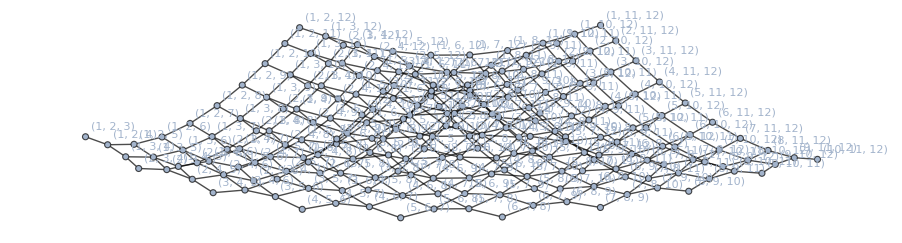

```mathematica
g=Import["C:\\Users\\Joel9\\Documents\\Investigacion Grafos\\Packing and 3token graphs\\Archivos Pn\\P12\\F3.gml"]
```

```mathematica
VertexList[g]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219}

```mathematica
m=TableForm[GraphDistanceMatrix[g],TableHeadings->{c=Style[#,Red]&/@%,c}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219
0 | 0 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 15 | 16 | 16 | 17 | 17 | 17 | 18 | 18 | 19 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 21 | 22 | 23 | 23 | 24 | 25 | 24 | 25 | 26 | 27
1 | 1 | 0 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 14 | 15 | 15 | 16 | 16 | 16 | 17 | 17 | 18 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 20 | 21 | 22 | 22 | 23 | 24 | 23 | 24 | 25 | 26
2 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 13 | 14 | 14 | 15 | 15 | 15 | 16 | 16 | 17 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
3 | 2 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 13 | 14 | 14 | 15 | 15 | 15 | 16 | 16 | 17 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
4 | 3 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 12 | 13 | 13 | 14 | 14 | 14 | 15 | 15 | 16 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
5 | 3 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 12 | 13 | 13 | 14 | 14 | 14 | 15 | 15 | 16 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
6 | 4 | 3 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
7 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
8 | 5 | 4 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
9 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
10 | 6 | 5 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
11 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
12 | 7 | 6 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 10 | 11 | 12 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
13 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
14 | 8 | 7 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 11 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 12 | 13 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
15 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
16 | 9 | 8 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 12 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 14 | 16 | 15 | 16 | 17 | 16 | 17 | 18
17 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 1 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
18 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 16 | 17
19 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 12 | 15 | 13 | 16 | 14 | 14 | 17 | 15 | 16 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
20 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
21 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
22 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
23 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
24 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
25 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
26 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
27 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
28 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
29 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
30 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
31 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
32 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
33 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
34 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 15 | 16
35 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 15 | 16
36 | 5 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
37 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
38 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
39 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
40 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
41 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
42 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
43 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
44 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
45 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
46 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
47 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
48 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
49 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 14 | 15
50 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 14 | 15
51 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
52 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
53 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
54 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
55 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
56 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
57 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
58 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
59 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
60 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
61 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
62 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
63 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
64 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
65 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
66 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
67 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
68 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
69 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
70 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
71 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
72 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
73 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
74 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
75 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
76 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
77 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
78 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
79 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
80 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
81 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
82 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
83 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
84 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
85 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 7 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
86 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
87 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
88 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 2 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
89 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 3 | 2 | 2 | 1 | 1 | 3 | 2 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
90 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 4 | 2 | 3 | 1 | 3 | 4 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
91 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 0 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
92 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 7 | 9 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 0 | 2 | 1 | 3 | 1 | 2 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 9 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 5 | 6 | 7 | 10 | 9 | 8 | 9 | 8 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 7 | 8 | 9 | 8 | 9 | 10 | 11
93 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 3 | 1 | 1 | 4 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
94 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 4 | 1 | 3 | 0 | 2 | 2 | 1 | 1 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 7 | 10 | 9 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10
95 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 0 | 2 | 3 | 1 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
96 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 2 | 0 | 3 | 1 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 6 | 7 | 8 | 7 | 8 | 9 | 10
97 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 3 | 0 | 2 | 1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 13 | 12 | 11 | 10 | 9 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 8 | 7 | 6 | 11 | 10 | 9 | 9 | 8 | 7 | 10 | 9 | 8 | 9
98 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 1 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 6 | 9 | 8 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9
99 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 0 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 5 | 10 | 9 | 8 | 8 | 7 | 6 | 9 | 8 | 7 | 8
100 | 6 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
101 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
102 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
103 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
104 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
105 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
106 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
107 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
108 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
109 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
110 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
111 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
112 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
113 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
114 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
115 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
116 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 1 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
117 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
118 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
119 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 1 | 0 | 1 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
120 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 1 | 0 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
121 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
122 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
123 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
124 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
125 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
126 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
127 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
128 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
129 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
130 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
131 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
132 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 1 | 3 | 4 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
133 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 1 | 4 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 5 | 6 | 7 | 6 | 7 | 8 | 9
134 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 8 | 7 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8
135 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 3 | 2 | 2 | 1 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 9 | 8 | 7 | 7 | 6 | 5 | 8 | 7 | 6 | 7
136 | 9 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
137 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
138 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
139 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
140 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
141 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
142 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
143 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
144 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 1 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
145 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
146 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
147 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 1 | 0 | 1 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
148 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 1 | 0 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
149 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
150 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
151 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
152 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
153 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
154 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
155 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
156 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
157 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
158 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
159 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
160 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
161 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 4 | 4 | 2 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 4 | 5 | 6 | 5 | 6 | 7 | 8
162 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 3 | 4 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 7 | 6 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7
163 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 4 | 3 | 3 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 8 | 7 | 6 | 6 | 5 | 4 | 7 | 6 | 5 | 6
164 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 12 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
165 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 1 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
166 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
167 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
168 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 1 | 0 | 1 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
169 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
170 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
171 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
172 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
173 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
174 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
175 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 13 | 11 | 12 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
176 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
177 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
178 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
179 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 13 | 11 | 12 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
180 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
181 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 6 | 7
182 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 12 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 3 | 6 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 3 | 4 | 5 | 4 | 5 | 6 | 7
183 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 4 | 5 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 6 | 5 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6
184 | 22 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 5 | 4 | 4 | 3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 7 | 6 | 5 | 5 | 4 | 3 | 6 | 5 | 4 | 5
185 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
186 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 13 | 11 | 12 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
187 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
188 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
189 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
190 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 13 | 11 | 14 | 12 | 13 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
191 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 13 | 11 | 12 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
192 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
193 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 6 | 7
194 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 14 | 12 | 13 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 12 | 12 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
195 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 12 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
196 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 5 | 6
197 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 14 | 12 | 13 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 6 | 6 | 4 | 7 | 5 | 6 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 5 | 6
198 | 22 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 5 | 6 | 4 | 5 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 5 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5
199 | 23 | 22 | 21 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 6 | 5 | 5 | 4 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 6 | 5 | 4 | 4 | 3 | 2 | 5 | 4 | 3 | 4
200 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 14 | 12 | 15 | 13 | 14 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 7 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
201 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 14 | 12 | 13 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 12 | 12 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
202 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 12 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
203 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 5 | 6
204 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 14 | 12 | 15 | 13 | 14 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 13 | 13 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
205 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 14 | 12 | 13 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 4 | 5 | 6
206 | 22 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 4 | 5
207 | 22 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 15 | 13 | 14 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 13 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 7 | 7 | 5 | 8 | 6 | 7 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 11 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 4 | 5
208 | 23 | 22 | 21 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 6 | 7 | 5 | 6 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 4 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4
209 | 24 | 23 | 22 | 22 | 21 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 7 | 6 | 6 | 5 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 5 | 4 | 3 | 3 | 2 | 1 | 4 | 3 | 2 | 3
210 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 15 | 13 | 16 | 14 | 15 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 13 | 14 | 14 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 12 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 15 | 14 | 13 | 12 | 11 | 10 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 0 | 1 | 2 | 2 | 3 | 4 | 3 | 4 | 5 | 6
211 | 22 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 15 | 13 | 14 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 13 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 12 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 11 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 3 | 4 | 5
212 | 23 | 22 | 21 | 21 | 20 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 10 |

```mathematica
Export["GDM_F3(P12).csv",m]
```

GDM_F3(P12).csv